```mathematica
h[p_,q_,ϕ_]:=Block[{hopping,pot},
(* hopping subdiagonal part *)
hopping=Table[{i,i+1}->-1.,{i,q-1}];
(* periodic boundary conditions *)
AppendTo[hopping,{1,q}->-1.];
(* convert to matrix *)
hopping=SparseArray[hopping,{q,q}];
(* symmetrize *)
hopping=hopping+Transpose[hopping];
(* diagonal part *)
pot=SparseArray[Table[{i,i}->2. Cos[2 π p i/q+ϕ],{i,q}],{q,q}];
Normal[pot+hopping]
]
```

```mathematica
(* choosing Fibonacci numbers as approximants *)
hfib[n_,ϕ_]:=h[Fibonacci[n-1],Fibonacci[n],ϕ];
SetAttributes[hfib,Listable];
```

```mathematica
n=50;
approxlist=Union[Flatten[Table[p/q,{q,n},{p,q}]]];
speclist=ParallelMap[Sort[Eigenvalues[#]]&,h[Numerator[#],Denominator[#],0]&/@approxlist];
```

```mathematica
div=10;
l=Length[speclist];
pts=Table[Point[{i/l,#/div}]&/@speclist[[i]],{i,l}]//Flatten;
```

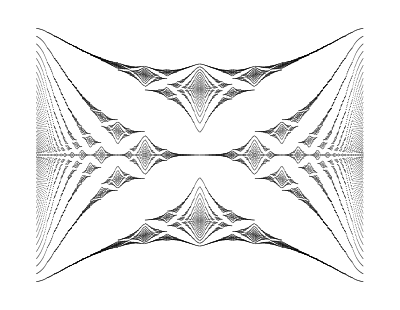

```mathematica
Graphics[{{PointSize[.001],pts}}]
```